-Graphics-

Make: Matrices & Geometry
Authors:  Bill Davis and Jerry Uhl  ©1996-2010
Publisher:  Make: Mathematics

# MGM.03 Using Aligners, Stretchers and Hangers to Make 2D Matrices Do What You Want LITERACY

Mathematica 8.0 Initializations

```mathematica
Off[General::"spell"];
  Off[General::"spell1"];  
Off[SingularValues::"deprec"];  

Needs["Units`"];  

SetOptions[ListAnimate, AnimationRepetitions -> 4];  
SetOptions[Animate, AnimationRepetitions -> 4];  
CMView={2.7,1.6,1.2};
```

#### Vector Drawer

```mathematica
(* :Date:  Copyright 1993-2011, Math Everywhere, Inc. 
*)
(*
Original Conception to create a vector drawer is due to Bill Davis.
Current code is by Bruce Carpenter.
*)
(*  :Drawbacks:  Since the vectors are drawn out of 
     context, the shapes of the arrowheads are only 
     correct with AspectRatio set to Automatic.
*)
```

```mathematica
BeginPackage["Vector3D`"];
```

```mathematica
Axes3D::usage="Axes3D[a, b] creates a Graphics3D object of cartesian axes with x, y, and z running from -a/3 to a, and with axes labels b units beyond the tips of the axes.  Axes3D[a] is Axes3D[a, a/8].";
Perpend::usage="Perpend[a] returns a unit vector which is perpendicular to the vector a.";
Vector::usage="Vector[a] produces a 2 or 3 dimensional vector from the origin to a. Arrow[a, Tail → tail] gives a vector from tail to a.";
CandMArrow::usage="CandMArrow[a, b] gives a 2D or 3D arrow from a to b.";
VectorHead::usage="VectorHead[a, vec] produces an arrowhead with its tip placed at the point a, pointing in the direction of the vector vec.";
Tail::usage="Tail → point puts the tail of the vector at point.";
Aperture::usage="Aperture is the ratio of the radius of the base to the length of the head of a vector.";
TipSize::usage="TipSize specifies an absolute size for the inner tip length of the head of a vector.";
TipRatio::usage="TipRatio is the ratio of the inner length of the arrowhead to the length of the shaft of a vector.";
HeadRatio::usage="HeadRatio is the ratio of the outer length of the arrowhead to the length of the shaft of a vector.";
HeadSize::usage="HeadSize specifies an absolute size for the head of a vector.";
ScaleFactor::usage="ScaleFactor specifies the amount to scale a vector in length and may be either a number or a pure function.";
ZeroVectorPointSize::usage="ZeroVectorPointSize is the size of the point used to represent a zero vector.";
Options[Vector]=Options[CandMArrow]=Options[VectorHead]={HeadRatio->0.18,TipRatio->0.14,Aperture->0.3,ScaleFactor->1,HeadType->Polygon,ShaftQ->True,EdgesQ->True,VectorColor->RGBColor[0,0,1],ShaftWidth->0.005,ZeroVectorPointSize->0.01};
Begin["`Private`"];
SetOptions[ParametricPlot,AspectRatio->Automatic];
SetOptions[Plot,AspectRatio->Automatic];
SetOptions[Graphics,AspectRatio->Automatic];
Axes3D[u_,v_]:=Graphics3D[{{Blue,Line[{{-u/3,0,0},{u,0,0}}]},Text["x",{u+v,0,0}],{Blue,Line[{{0,-u/3,0},{0,u,0}}]},Text["y",{0,u+v,0}],{Blue,Line[{{0,0,-u/3},{0,0,u}}]},Text["z",{0,0,u+v}]}];
Axes3D[u_]:=Axes3D[u,u/8];
Perpend[a_?VectorQ]:=Normalize[{a⟦2⟧,-a⟦1⟧}]/;Length[a]==2;
Perpend[a_?VectorQ]:=Normalize[If[a⟦1⟧==0,{1,0,0},{a⟦2⟧,-a⟦1⟧,0}]]/;Length[a]==3;
Base3D=Table[{Cos[(2 k π)/8.],Sin[(2 k π)/8.]},{k,0,8}];
CandMArrow[from_?VectorQ,to_?VectorQ,opts___]:=Module[{sq,sw,ht,hs,hr,tr,ap,sf,vc,zvps,diff=to-from,tip},{sq,sw,ht,hs,hr,ts,tr,ap,sf,vc,zvps}={ShaftQ,ShaftWidth,HeadType,HeadSize,HeadRatio,TipSize,TipRatio,Aperture,ScaleFactor,VectorColor,ZeroVectorPointSize}/.{opts}/.Options[Vector];If[from==to,Return[Graphics[{PointSize[zvps],vc,Point[from]}]]];diff=If[NumberQ[N[sf]],sf diff,sf[diff]];tip=from+diff;If[NumberQ[hs],hr=hs/Norm[diff];tr=0.75 hr];If[NumberQ[ts],tr=ts/Norm[diff]];Graphics[{If[sq,{vc,Thickness[sw],Line[{from,tip-tr diff}]},{}],With[{trans=ap hr Norm[diff] Perpend[diff]},{vc,Thickness[sw],ht[{tip,tip-hr diff+trans,tip-tr diff,tip-hr diff-trans,tip}]}]}]]/;Length[from]==Length[to]==2
CandMArrow[from_?VectorQ,to_?VectorQ,opts___]:=Module[{sq,eq,sw,hs,hr,tr,ap,sf,vc,zvps,diff=to-from,tip},{sq,eq,sw,hs,hr,ap,sf,vc,zvps}={ShaftQ,EdgesQ,ShaftWidth,HeadSize,HeadRatio,Aperture,ScaleFactor,VectorColor,ZeroVectorPointSize}/.{opts}/.Options[Vector];If[from==to,Return[Graphics3D[{PointSize[zvps],vc,Point[from]}]]];diff=If[NumberQ[N[sf]],sf diff,sf[diff]];tip=from+diff;If[NumberQ[hs],hr=hs/Norm[diff]];tr=hr/2;Graphics3D[{If[sq,{vc,Thickness[sw],Line[{from,tip-tr diff}]},{}],If[eq,{},EdgeForm[]],{SurfaceColor[vc],With[{temp=Perpend[diff]},(Polygon[Append[#1,tip]]&)/@Partition[(tip-hr diff+#1&)/@((ap hr Norm[diff] Base3D).{temp,Normalize[temp×diff]}),2,1]]}}]]/;Length[from]==Length[to]==3
Vector[a_,Tail->b_,opts___]:=CandMArrow[b,a+b,opts]
Vector[a_,opts___]:=CandMArrow[Table[0,{Length[a]}],a,opts]
VectorHead[a_,b_,opts___]:=CandMArrow[a-b,a,ShaftQ->False,opts];
End[];
EndPackage[];
```

```mathematica
Graphics`Colors`GosiaGreen=RGBColor[0, 0.392187, 0];
```

#### ThreeAxes[u,v]

```mathematica
ThreeAxes[u_,v_]:=Graphics3D[{{Blue,Line[{{-u,0,0},{u,0,0}}]},Text["x",{u+v,0,0}],{Blue,Line[{{0,-u,0},{0,u,0}}]},Text["y",{0,u+v,0}],{Blue,Line[{{0,0,0},{0,0,u}}]},Text["z",{0,0,u+v}]}];
ThreeAxes[u_]:=ThreeAxes[u,u/8];
ThreeAxes::"usage"="ThreeAxes[a,b] makes a standard cartesian axis graphics object with x, y, and z running from -a to a, and with axis labels b units beyond the tips of the axes.  ThreeAxes[a] is ThreeAxes[a,a/8].";
```

### What you should be able to handle when you are away from the machine.

#### L.1)

Here are the x and y axis unit vectors:

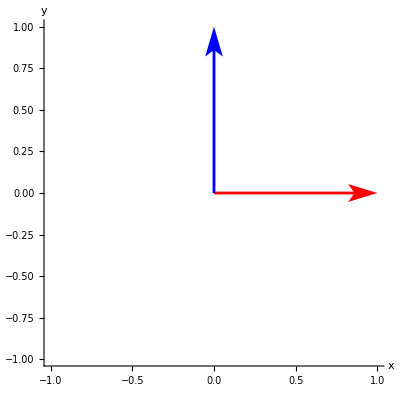

```mathematica
xyunits = Show[
     Vector[{1,0},Tail->{0,0},VectorColor->Red],
      Vector[{0,1},Tail->{0,0},VectorColor->Blue], 
   PlotRange->{{-1,1},{-1,1}},Axes->True,AxesLabel->{"x","y"}]
```

Here's a perpendicular frame:

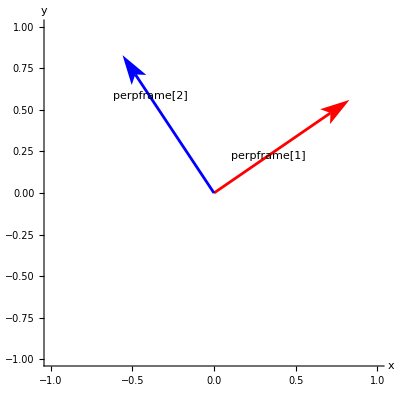

```mathematica
s=Random[Real,{π/16,0.3 π}];
Clear[perpframe];
{perpframe[1],perpframe[2]}={{Cos[s],Sin[s]},{Cos[s+π/2],Sin[s+π/2]}};
frameplot=Show[Vector[perpframe[1],Tail->{0,0},VectorColor->Red],Vector[perpframe[2],Tail->{0,0},VectorColor->Blue],Graphics[Text["perpframe[1]",0.4 perpframe[1]]],Graphics[Text["perpframe[2]",0.7 perpframe[2]]],PlotRange->{{-1,1},{-1,1}},Axes->True,AxesLabel->{"x","y"}]
```

When you hit the x-y axis unit vectors with the hanger corresponding to the this perpendicular frame, you get one of the following outcomes:

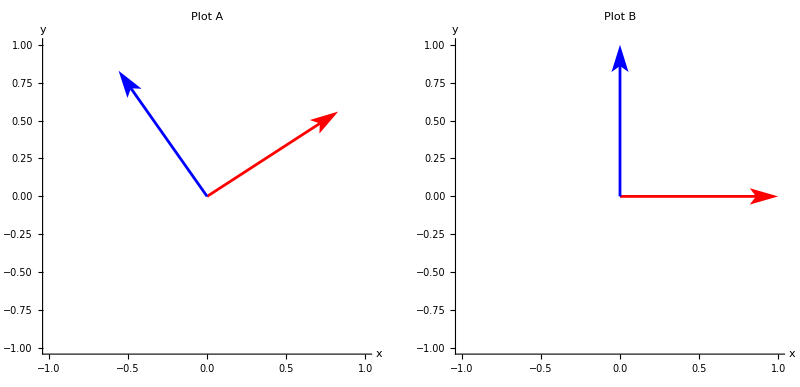

```mathematica
original = Show[
     Vector[perpframe[1],Tail->{0,0},VectorColor->Red],
      Vector[perpframe[2],Tail->{0,0},VectorColor->Blue], 
     PlotRange->{{-1,1},{-1,1}},Axes->True,AxesLabel->{"x","y"},PlotLabel->"Plot A"];
xyunits = Show[
     Vector[{1,0},Tail->{0,0},VectorColor->Red],
      Vector[{0,1},Tail->{0,0},VectorColor->Blue], 
   PlotRange->{{-1,1},{-1,1}},Axes->True,AxesLabel->{"x","y"},PlotLabel->"Plot B"];
GraphicsRow[{original,xyunits}]
```

The correct plot is Plot.......

#### L.2)

Here's a perpendicular frame:

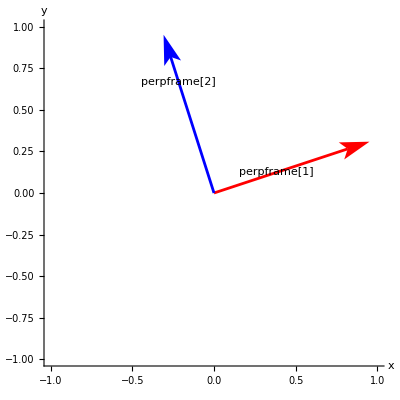

```mathematica
s=Random[Real,{π/16,0.3 π}];
Clear[perpframe];
{perpframe[1],perpframe[2]}={{Cos[s],Sin[s]},{Cos[s+π/2],Sin[s+π/2]}};
frameplot=Show[Vector[perpframe[1],Tail->{0,0},VectorColor->Red],Vector[perpframe[2],Tail->{0,0},VectorColor->Blue],Graphics[Text["perpframe[1]",0.4 perpframe[1]]],Graphics[Text["perpframe[2]",0.7 perpframe[2]]],PlotRange->{{-1,1},{-1,1}},Axes->True,AxesLabel->{"x","y"}]
```

When you hit this perpendicular frame with the aligner corresponding to the same perpendicular frame, you get one of the following outcomes:

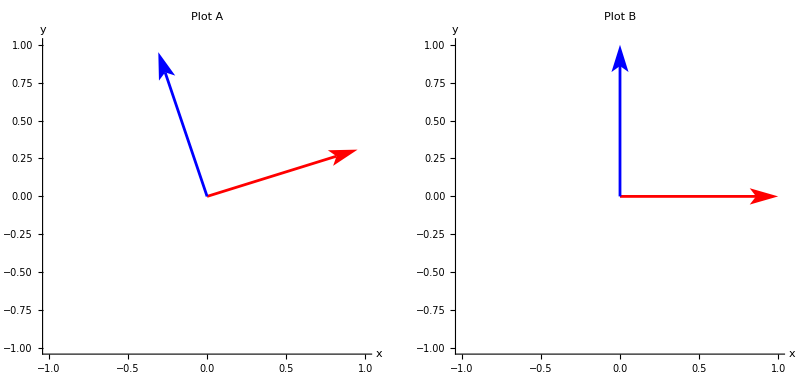

```mathematica
original = Show[
     Vector[perpframe[1],Tail->{0,0},VectorColor->Red],
      Vector[perpframe[2],Tail->{0,0},VectorColor->Blue], 
     PlotRange->{{-1,1},{-1,1}},Axes->True,AxesLabel->{"x","y"},PlotLabel->"Plot A"];
xyunits = Show[
     Vector[{1,0},Tail->{0,0},VectorColor->Red],
      Vector[{0,1},Tail->{0,0},VectorColor->Blue], 
   PlotRange->{{-1,1},{-1,1}},Axes->True,AxesLabel->{"x","y"},PlotLabel->"Plot B"];
GraphicsRow[{original,xyunits}]
```

The correct plot is Plot.......

#### L.3)

Agree or disagree:
When you hit a 2D perpendicular frame with a 2D matrix, you get another perpendicular frame.
Agree...............   Disagree.............

#### L.4)

Here's a perpendicular frame

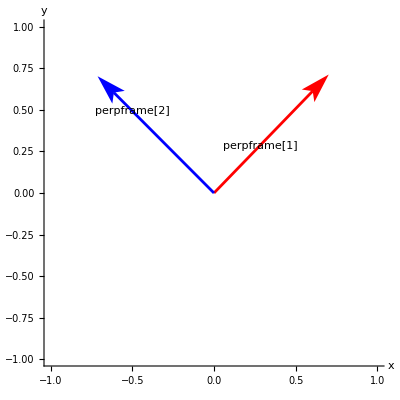

```mathematica
s=Random[Real,{-π/3,0.4 π}];
Clear[perpframe];
{perpframe[1],perpframe[2]}={{Cos[s],Sin[s]},{Cos[s+π/2],Sin[s+π/2]}};
frameplot=Show[Vector[perpframe[1],Tail->{0,0},VectorColor->Red],Vector[perpframe[2],Tail->{0,0},VectorColor->Blue],Graphics[Text["perpframe[1]",0.4 perpframe[1]]],Graphics[Text["perpframe[2]",0.7 perpframe[2]]],PlotRange->{{-1,1},{-1,1}},Axes->True,AxesLabel->{"x","y"}]
```

Here is an ellipse:

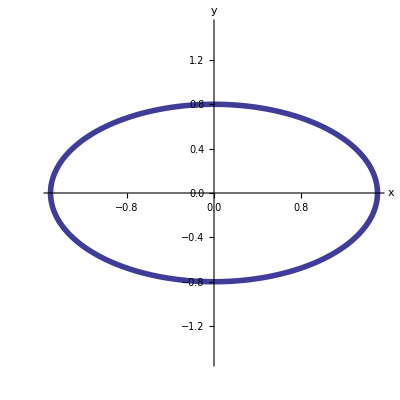

```mathematica
ParametricPlot[{1.5 Cos[t],0.8 Sin[t]},{t,0,2 Pi},PlotStyle->Thickness[0.01],AxesLabel->{"x","y"},PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
```

When you hit this ellipse with the hanger corresponding to the perpendicular frame plotted above, you get one of the following outcomes:

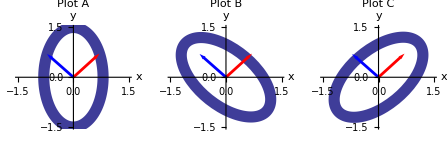

```mathematica
frameplot = Show[
     Vector[perpframe[1],Tail->{0,0},VectorColor->Red],
      Vector[perpframe[2],Tail->{0,0},VectorColor->Blue]]; 
 
Cplot= ParametricPlot[1.5 Cos[t] perpframe[1] +0.8 Sin[t] perpframe[2],{t,0,2 Pi},PlotStyle->Thickness[0.02],AxesLabel->{"x","y"},PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotLabel->"Plot C"];
Cplotframe = Show[Cplot,frameplot];
Bplot = 
	ParametricPlot[1.5 Cos[t] perpframe[2] +0.8 Sin[t] perpframe[1],{t,0,2 Pi},PlotStyle->Thickness[0.02],AxesLabel->{"x","y"},PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotLabel->"Plot B"];
Bplotframe = Show[Bplot,frameplot];
Aplot = ParametricPlot[{0.8 Cos[t] ,1.5 Sin[t]} ,{t,0,2 Pi},PlotStyle->Thickness[0.02],AxesLabel->{"x","y"},PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotLabel->"Plot A"];
Aplotframe = Show[Aplot,frameplot];
GraphicsRow[{Aplotframe,Bplotframe,Cplotframe}]
```

The correct plot is Plot.......

#### L.5)

Here's a perpendicular frame shown with a certain ellipse:

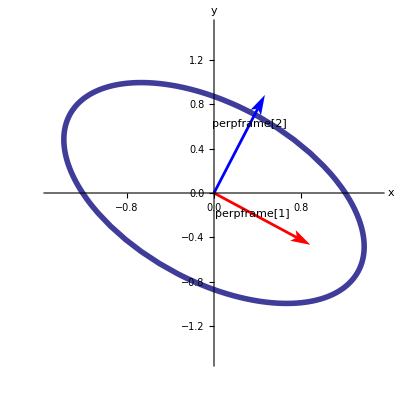

```mathematica
s=Random[Real,{-π/3,0.4 π}];
Clear[perpframe];
{perpframe[1],perpframe[2]}={{Cos[s],Sin[s]},{Cos[s+π/2],Sin[s+π/2]}};
frameplot=Show[Vector[perpframe[1],Tail->{0,0},VectorColor->Red],Vector[perpframe[2],Tail->{0,0},VectorColor->Blue],Graphics[Text["perpframe[1]",0.4 perpframe[1]]],Graphics[Text["perpframe[2]",0.7 perpframe[2]]]];
ellipse=ParametricPlot[1.5 Cos[t] perpframe[1]+0.8 Sin[t] perpframe[2],{t,0,2 π},PlotStyle->Thickness[0.01],AxesLabel->{"x","y"},PlotRange->{{-1.5,1.5},{-1.5,1.5}}];
Show[ellipse,frameplot]
```

When you hit this ellipse with the aligner corresponding to the perpendicular frame plotted above, you get one of the following outcomes:

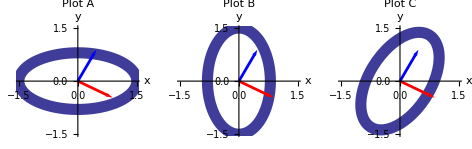

```mathematica
frameplot = Show[
     Vector[perpframe[1],Tail->{0,0},VectorColor->Red],
      Vector[perpframe[2],Tail->{0,0},VectorColor->Blue]]; 
 
Cplot= ParametricPlot[1.5 Cos[t] perpframe[2] +0.8 Sin[t] perpframe[1],{t,0,2 Pi},PlotStyle->Thickness[0.02],AxesLabel->{"x","y"},PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotLabel->"Plot C"];
Cplotframe = Show[Cplot,frameplot];
Bplot = 
	ParametricPlot[{0.8 Cos[t] ,1.5 Sin[t]},{t,0,2 Pi},PlotStyle->Thickness[0.02],AxesLabel->{"x","y"},PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotLabel->"Plot B"];
Bplotframe = Show[Bplot,frameplot];
Aplot = ParametricPlot[{1.5 Cos[t] ,0.8 Sin[t]} ,{t,0,2 Pi},PlotStyle->Thickness[0.02],AxesLabel->{"x","y"},PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotLabel->"Plot A"];
Aplotframe = Show[Aplot,frameplot];
GraphicsRow[{Aplotframe,Bplotframe,Cplotframe}]
```

The correct plot is Plot.......

#### L.6)

Here's a 2D perpendicular frame 
{perpframe[1],perpframe[2]}={{(√3)/2,1/2},{-1/2,(√3)/2}}
Given that the hanger corresponding to this perpendicular frame is
          hanger=(a | b
c | d),
fill in the appropriate values: 
a = ................... b = ...................
c = ................... d = ...................

#### L.7)

Here's a 2D perpendicular frame:
{perpframe[1],perpframe[2]}={{1/2,(√3)/2},{-(√3)/2,1/2}}
Given that the aligner corresponding to this perpendicular frame is
           aligner=(a | b
c | d),
fill in the appropriate values: 
a = ................... b = ...................
c = ................... d = ...................

#### L.8)

Here's a cleared 2D perpendicular frame:

{perpframe[1],perpframe[2]}={{Cos[s],Sin[s]},{-Sin[s],Cos[s]}}

Here is a point in usual xy coordinates:

```mathematica
{0.3  Random[Integer,{1,9}],0.2  Random[Integer,{-9,9}]}
```

{1.8,-0.2}

The perpendicular frame coordinates (for the perpendicular frame specified above)  {u,v} of this point are given by
u = ............................................................................
v = ............................................................................

#### L.9)

Here's a cleared 2D perpendicular frame:

{perpframe[1],perpframe[2]}={{Cos[s],Sin[s]},{-Sin[s],Cos[s]}}

Here is a point with usual xy coordinates:

```mathematica
{x,y} ={0.3  Random[Integer,{-9,9}],0.2  Random[Integer,{1,9}]}
```

{-2.1,0.2}

Fill the blank below with either the word "aligner" or "hanger."
I can calculate the perpframe coordinates of this point by hitting {x,y} with the 
 .........................   for this perpendicular frame.

#### L.10)

Here's a cleared 2D perpendicular frame:

{perpframe[1],perpframe[2]}={{Cos[s],Sin[s]},{-Sin[s],Cos[s]}}

Here is a point with usual perpframe coordinates:

```mathematica
{u,v} ={0.3  Random[Integer,{1,9}],0.2  Random[Integer,{1,9}]}
```

{2.7,0.8}

Fill the blank below with either the word "aligner" or "hanger."
I can calculate the usual xy coordinates of this point by hitting {u,v} with the 
 .........................   for this perpendicular frame.

#### L.11)

Here is a perpendicular frame and a curve:

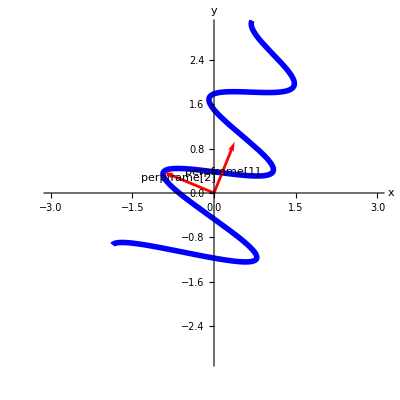

```mathematica
s=Random[Real,{0.2,1.5}];
Clear[perpframe];
{perpframe[1],perpframe[2]}=N[{{Cos[s],Sin[s]},{-Sin[s],Cos[s]}}];
frameplot=Show[Table[Vector[perpframe[k],Tail->{0,0},VectorColor->Red],{k,1,2}],Graphics[Text["perpframe[1]",0.4 perpframe[1]]],Graphics[Text["perpframe[2]",0.7 perpframe[2]]],Axes->True,AxesLabel->{"x","y"}];
Clear[x,y,t];
{tlow,thigh}={-π/2,π};
{x[t_],y[t_]}=t perpframe[1]+E^(-0.2 t) Cos[4 t] perpframe[2];
curveplot=ParametricPlot[{x[t],y[t]},{t,tlow,thigh},PlotStyle->{{Thickness[0.01],Blue}},AxesLabel->{"x","y"}];
Show[curveplot,frameplot,PlotRange->{{-3,3},{-3,3}}]
```

Here is what you get when you hit this curve with a certain matrix A:

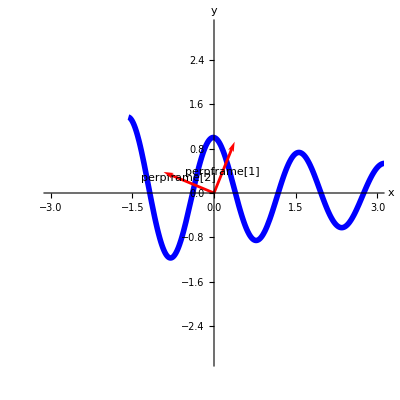

```mathematica
A = {perpframe[1],perpframe[2]};
hitcurveplot = ParametricPlot[A.{x[t],y[t]},{t,tlow,thigh},
       PlotStyle->{{Thickness[0.01],Blue}},AxesLabel->{"x","y"}];
Show[hitcurveplot,frameplot,PlotRange->{{-3,3},{-3,3}}]
```

Given that this matrix A is either the aligner or the hanger based on the plotted perpendicular frame, which is it:
The aligner?
The hanger?

#### L.12)

Here is a perpendicular frame and a curve:

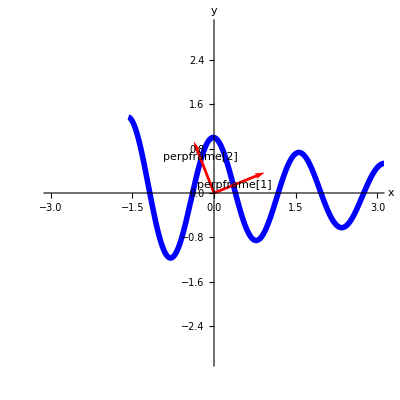

```mathematica
s=Random[Real,{0.2,0.6}];
Clear[perpframe];
{perpframe[1],perpframe[2]}=N[{{Cos[s],Sin[s]},{-Sin[s],Cos[s]}}];
frameplot=Show[Table[Vector[perpframe[k],Tail->{0,0},VectorColor->Red],{k,1,2}],Graphics[Text["perpframe[1]",0.4 perpframe[1]]],Graphics[Text["perpframe[2]",0.7 perpframe[2]]],Axes->True,AxesLabel->{"x","y"}];
Clear[x,y,t];
{tlow,thigh}={-π/2,π};
{x[t_],y[t_]}={t,E^(-0.2 t) Cos[4 t]};
curveplot=ParametricPlot[{x[t],y[t]},{t,tlow,thigh},PlotStyle->{{Thickness[0.01],Blue}},AxesLabel->{"x","y"}];
Show[curveplot,frameplot,PlotRange->{{-3,3},{-3,3}}]
```

Here is what you get when you hit this curve with a certain matrix A:

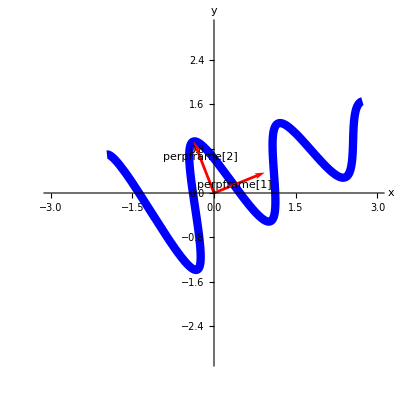

```mathematica
A = Transpose[{perpframe[1],perpframe[2]}];
hitcurveplot = ParametricPlot[A.{x[t],y[t]},{t,tlow,thigh},
       PlotStyle->{{Thickness[0.015],Blue}},AxesLabel->{"x","y"}];
Show[hitcurveplot,frameplot,PlotRange->{{-3,3},{-3,3}}]
```

Given that this matrix A is either the aligner or the hanger based on the plotted perpendicular frame, which is it:
The aligner?
The hanger?

#### L.13)

Here's a random 2D matrix 
              A = hanger.stretcher.aligner 
made through matrix maker ingredients:

```mathematica
Clear[alignerframe];
s=Random[Real,{-1.5,1.5}];
{alignerframe[1],alignerframe[2]}=N[{{Cos[s],Sin[s]},{Cos[s+π/2],Sin[s+π/2]}}];
aligner={alignerframe[1],alignerframe[2]};
{xstretch,ystretch}={0.5 Random[Integer,{5,10}],0.2 Random[Integer,{5,10}]};
stretcher={{xstretch,0},{0,ystretch}};
Clear[hangerframe];
s=Random[Real,{-1.5,1.5}];
{hangerframe[1],hangerframe[2]}=N[{{Cos[s],Sin[s]},{Cos[s+π/2],Sin[s+π/2]}}];
hanger=Transpose[{hangerframe[1],hangerframe[2]}];
A=hanger.(stretcher.aligner);
MatrixForm[A]
```

(2.58532 | -1.28796
-0.411105 | 2.64164)

When you hit the unit circle centered at {0,0} with A you get this ellipse:

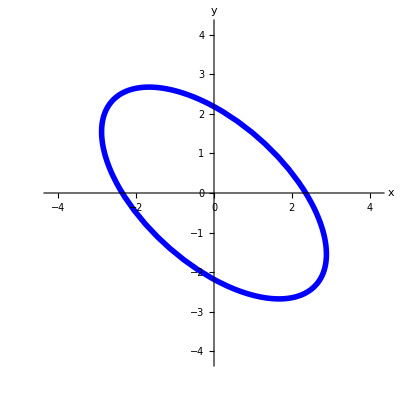

```mathematica
Clear[x,y,t];
{x[t_],y[t_]}={Cos[t],Sin[t]};
{tlow,thigh}={0,2 π};
ranger=1.2 Max[{xstretch,ystretch,1}];
ellipseplot=ParametricPlot[A.{x[t],y[t]},{t,tlow,thigh},PlotStyle->{{Thickness[0.01],Blue}},PlotRange->{{-ranger,ranger},{-ranger,ranger}},AxesLabel->{"x","y"}]
```

Agree or disagree with each of the following statements:

1) When you change the stretcher by going with new stretch factors and replot, you are guaranteed to get the same physical ellipse as plotted above.
Agree...............   Disagree.............

2) When you change the aligner by going with a different aligner frame and replot, you are guaranteed to get the same physical ellipse as plotted above.
Agree...............   Disagree.............

3) When you change the hanger by going with a different hanger frame and replot, you are guaranteed to get the same physical ellipse as plotted above.
Agree...............   Disagree.............

#### L.14.i)

Here's a random 2D matrix 
              A = hanger.stretcher.aligner 
made through matrix maker ingredients.
The aligner is:

```mathematica
Clear[alignerframe];
s=Random[Real,{-1.5,1.5}];
{alignerframe[1],alignerframe[2]}=N[{{Cos[s],Sin[s]},{Cos[s+π/2],Sin[s+π/2]}}];
aligner={alignerframe[1],alignerframe[2]};
MatrixForm[aligner]
```

(0.916981 | -0.398932
0.398932 | 0.916981)

The stretcher is:

```mathematica
{xstretch,ystretch}={0.5 Random[Integer,{5,10}],0.2 Random[Integer,{5,10}]};
stretcher={{xstretch,0},{0,ystretch}};
MatrixForm[stretcher]
```

(4. | 0
0 | 1.8)

The hanger is:

```mathematica
Clear[hangerframe];
s=Random[Real,{-1.5,1.5}];
{hangerframe[1],hangerframe[2]}=N[{{Cos[s],Sin[s]},{Cos[s+π/2],Sin[s+π/2]}}];
hanger=Transpose[{hangerframe[1],hangerframe[2]}];
MatrixForm[hanger]
```

(0.69122 | -0.722644
0.722644 | 0.69122)

The resulting matrix 
             A = hanger.stretcher.aligner 
is:

```mathematica
A=hanger.(stretcher.aligner);
MatrixForm[A]
```

(2.01643 | -2.29577
3.14695 | -0.0122396)

When you hit the unit circle centered at {0,0} with A you get this ellipse:

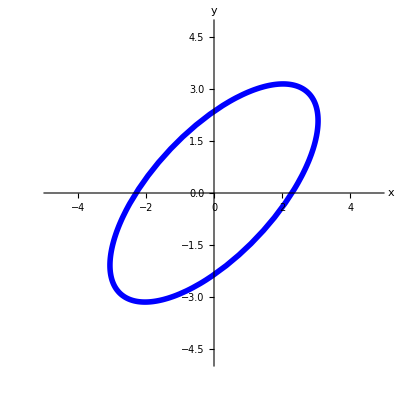

```mathematica
Clear[x,y,t];
{x[t_],y[t_]}={Cos[t],Sin[t]};
{tlow,thigh}={0,2 π};
ranger=1.2 Max[{xstretch,ystretch,1}];
ellipseplot=ParametricPlot[A.{x[t],y[t]},{t,tlow,thigh},PlotStyle->{{Thickness[0.01],Blue}},PlotRange->{{-ranger,ranger},{-ranger,ranger}},AxesLabel->{"x","y"}]
```

Look at this plot of the hanger frame and its negatives:

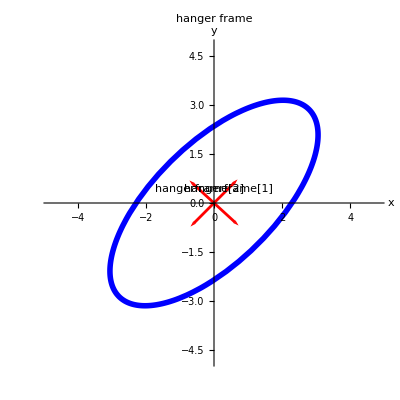

```mathematica
Show[ellipseplot,Vector[hangerframe[1],Tail->{0,0},VectorColor->Red],Vector[-hangerframe[1],Tail->{0,0},VectorColor->Red],Vector[hangerframe[2],Tail->{0,0},VectorColor->Red],Vector[-hangerframe[2],Tail->{0,0},VectorColor->Red],Graphics[Text["hangerframe[1]",0.6 hangerframe[1]]],Graphics[Text["hangerframe[2]",0.6 hangerframe[2]]],Axes->True,AxesLabel->{"x","y"},PlotRange->{{-ranger,ranger},{-ranger,ranger}},PlotLabel->"hanger frame"]
```

Do you think the outcome is an accident? 
Yes.......
No........

#### L.14.ii)

Stay with the same set up as in part i) and look at this plot in which the unit hanger frame vectors have been multiplied by their associated stretch factors:

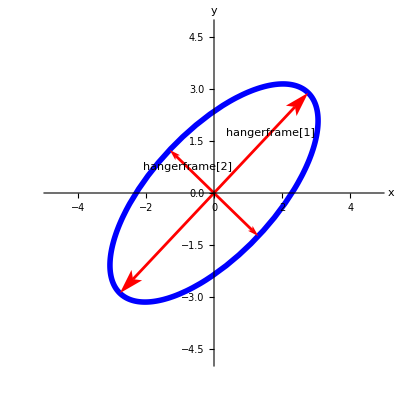

```mathematica
lastplot=Show[ellipseplot,Vector[xstretch hangerframe[1],Tail->{0,0},VectorColor->Red],Vector[-xstretch hangerframe[1],Tail->{0,0},VectorColor->Red],Vector[ystretch hangerframe[2],Tail->{0,0},VectorColor->Red],Vector[-ystretch hangerframe[2],Tail->{0,0},VectorColor->Red],Graphics[Text["hangerframe[1]",0.6 xstretch hangerframe[1]]],Graphics[Text["hangerframe[2]",0.6 ystretch hangerframe[2]]],Axes->True,AxesLabel->{"x","y"},PlotRange->{{-ranger,ranger},{-ranger,ranger}}]
```

Do you think the outcome is an accident? 
Yes.........
No.........
If not, why not?

#### L.14.iii)

Here's another look at the plot in part ii) above:

```mathematica
Show[lastplot]
```

-Graphics-

And look at the stretch factors used to make A:

```mathematica
{xstretch,ystretch}
```

{4.,1.8}

Fill the blanks.
The length of the long axis of this ellipse measures out to ...........
The length of the short axis of this ellipse measures out to ...........
The area enclosed by this ellipse measures out to.........

#### L.15)

For what kind of perpendicular frames is the corresponding hanger guaranteed to be a rotation matrix?
For what kind of perpendicular frames is the corresponding aligner guaranteed to be a rotation matrix?

#### L.16)

Go with the hanger and the aligner corresponding to a given 2D perpendicular frame.
When you multiply out 
            hanger.aligner, 
you get
             hanger.aligner =(□ | □
□ | □).
(Fill the boxes.)

#### L.17)

If (a | b
c | d) is the aligner corresponding to a given perpendicular frame, then the hanger corresponding to the same perpendicular frame is  hanger = (□ | □
□ | □).
(Fill the boxes.)

#### L.18)

You are given a perpendicular frame {perpframe[1],perpframe[2]}. Explain how you go about making a matrix A so that
          A.perpframe[1]=3.2 perpframe[1]
and
          A.perpframe[2]=0.5 perpframe[2].

#### L.19)

You are given a perpendicular frame {perpframe[1],perpframe[2]}. Explain how you  go about making a matrix A so that
          A.perpframe[1]=0.7 perpframe[2]
and
          A.perpframe[2]=1.3 perpframe[1].

#### L.20)

When you are making a matrix 
           A = hanger.stretcher.aligner,
what do you do so to be sure that A is invertible?

#### L.21)

You are given a line through {0,0} in the direction of a unit vector{a,b}.
Define ( by filling the boxes) 
            aligner =(□ | □
□ | □), 
            stretcher = (□ | □
□ | □)  and 
            hanger =(□ | □
□ | □)
so that when you hit any {x,y} with 
            A=hanger.stretcher.aligner, 
you get the point on the line closest to {x,y}.

#### Tip: The vector {-b,a} is a unit vector perpendicular to the line.

#### L.22)

You make a 2D matrix A by choosing a perpendicular frame to define your aligner, choosing another perpendicular frame for your hanger and two stretch factors xstretch and ystretch and then putting

             A =  hanger.(xstretch | 0
0 | ystretch). aligner.
             
Using this, you can compute A^tvia the formula:

a)  A^t =  aligner.(xstretch | 0
0 | ystretch). hanger    
        
b)  A^t =  hanger^t.(ystretch | 0
0 | xstretch). aligner^t

c)  A^t =  aligner^t.(ystretch | 0
0 | xstretch). hanger^t      

d)  A^t =  aligner^t.(xstretch | 0
0 | ystretch). hanger^t

My choice is ...........

#### L.23)

You make a 2D matrix A by choosing a perpendicular frame to define your aligner, choosing another perpendicular frame for your hanger and two stretch factors xstretch and ystretch and then putting

             A =  hanger.(xstretch | 0
0 | ystretch). aligner.
             
Using this, you can compute A^-1via the formula:

a)  A^-1 =  aligner.(1/xstretch | 0
0 | 1/ystretch). hanger       
b)  A^-1 =  hanger^t.(1/xstretch | 0
0 | 1/ystretch). aligner^t
 
c)  A^-1 =  aligner^t.(1/ystretch | 0
0 | 1/xstretch). hanger^t    
d)  A^-1 =  aligner^t.(1/xstretch | 0
0 | 1/ystretch). hanger^t

My choice is ...........

#### L.24)

You make a 2D matrix A by choosing a perpendicular frame to define your aligner, choosing another perpendicular frame for your hanger and two stretch factors xstretch and ystretch and the putting

             A =  aligner.(xstretch | 0
0 | ystretch). hanger.
             
If  xstretch≠0  and  ystretch≠0 , then you are guaranteed that given any 2D vector Y, there is exactly one 2D vector X with A.X=Y.
Agree........................................
Disagree........................................

#### L.25.i)

Here's a random matrix made with matrix maker ingredients

```mathematica
Clear[alignerframe];
s = Random[Real,{-Pi/2,Pi/2}];
{alignerframe[1],alignerframe[2]} = 
           N[{{Cos[s],Sin[s]},{Cos[s + Pi/2],Sin[s + Pi/2]}}];
aligner = {alignerframe[1],alignerframe[2]};

{xstretch,ystretch} = {0.5 Random[Integer,{4,8}],0.2 Random[Integer,{3,7}]};
stretcher = {{xstretch,0},{0,ystretch}};

Clear[hangerframe];
s = Random[Real,{-Pi/2,Pi/2}];;
{hangerframe[1],hangerframe[2]} = 
           N[{{Cos[s],Sin[s]},{Cos[s + Pi/2],Sin[s + Pi/2]}}];
hanger = Transpose[{hangerframe[1],hangerframe[2]}];
A = hanger.stretcher.aligner;
MatrixForm[A]
```

(0.618891 | -2.27356
0.6126 | 0.981139)

Here are the ellipses you get what you get when you hit the unit circle centered at {0,0} with this matrix and its inverse:

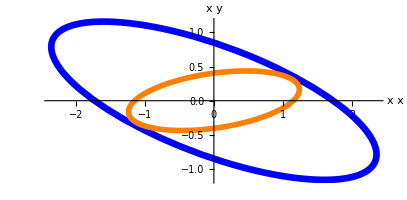

```mathematica
Clear[x,y,t,s];
{tlow,thigh}={0,2 π};
{x[t_],y[t_]}={Cos[t],Sin[t]};
Clear[hitplotter,hitpointplotter,pointcolor,actionarrows,matrix2D];
Ahit=ParametricPlot[A.{x[t],y[t]},{t,tlow,thigh},PlotStyle->{{Thickness[0.012],Blue}},AxesLabel->{"x","y"}x];
invAhit=ParametricPlot[Inverse[A].{x[t],y[t]},{t,tlow,thigh},PlotStyle->{{Thickness[0.01],Orange}},AxesLabel->{"x","y"}];
Show[Ahit,invAhit,PlotRange->All]
```

Put
      a = measurement of area enclosed by one of these ellipses
      b =   measurement of area enclosed by the other ellipse .
Without getting your hands dirty, calculate the product 
        a times b.

#### L.25.ii)

The stretch factors used to make the matrix in part i) are:

```mathematica
{xstretch,ystretch}
```

{2.5,0.8}

Use what you see to measure the area enclosed by each ellipse.

#### L.26.i)

Here's a random matrix made with matrix maker ingredients

```mathematica
Clear[alignerframe];
s = Random[Real,{-Pi/2,Pi/2}];
{alignerframe[1],alignerframe[2]} = 
           N[{{Cos[s],Sin[s]},{Cos[s + Pi/2],Sin[s + Pi/2]}}];
aligner = {alignerframe[1],alignerframe[2]};

{xstretch,ystretch} = {0.4 Random[Integer,{3,5}],0.3 Random[Integer,{1,3}]};
stretcher = {{xstretch,0},{0,ystretch}};

Clear[hangerframe];
s = Random[Real,{-Pi/2,Pi/2}];;
{hangerframe[1],hangerframe[2]} = 
           N[{{Cos[s],Sin[s]},{Cos[s + Pi/2],Sin[s + Pi/2]}}];
hanger = Transpose[{hangerframe[1],hangerframe[2]}];
A = hanger.stretcher.aligner;
MatrixForm[A]
```

(1.02139 | 0.593472
-0.00805365 | 1.40517)

Here is the square with corners at {-1,-1}, {1,-1},{1,1}, and {-1,1}:

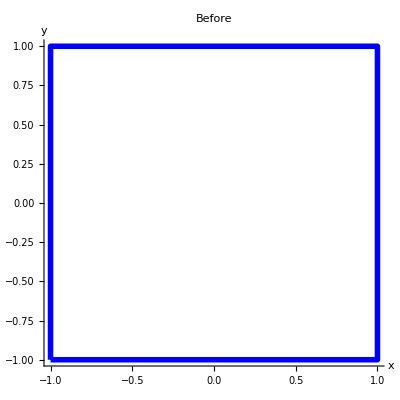

```mathematica
Show[Graphics[{Thickness[0.01],Blue,Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}]}],PlotRange->All,Axes->True,AxesLabel->{"x","y"},PlotLabel->"Before"]
```

Here are the parallelograms you get what you get when you hit this square with this matrix and its transpose:

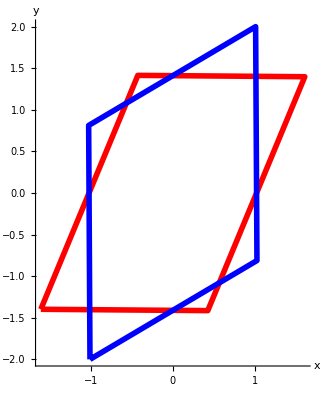

```mathematica
Ahit = Graphics[{Thickness[0.01],Red,Line[{A.{-1,-1},A.{1,-1},A.{1,1},A.{-1,1},A.{-1,-1}}]}];
B = Transpose[A];
transAhit =  Graphics[{Thickness[0.01],Blue,Line[{B.{-1,-1},B.{1,-1},B.{1,1},B.{-1,1},B.{-1,-1}}]}];

Show[Ahit,transAhit,PlotRange->All, Axes->True,AxesLabel->{"x","y"}]
```

Express the measurement of area enclosed by one of these parallelograms in terms of the measurement of the area enclosed by the other.

#### L.26.ii)

The stretch factors used to make the matrix in part i) are:

```mathematica
{xstretch,ystretch}
```

{1.6,0.9}

Use what you see to measure the area enclosed by each parallelogram.

#### L.27.i)

Here's a random 2D matrix 
              A = hanger.stretcher.aligner 
made through matrix maker ingredients.
The aligner is:

```mathematica
Clear[alignerframe];
s=Random[Real,{-1.5,1.5}];
{alignerframe[1],alignerframe[2]}=N[{{Cos[s],Sin[s]},{Cos[s+π/2],Sin[s+π/2]}}];
aligner={alignerframe[1],alignerframe[2]};
MatrixForm[aligner]
```

(0.860305 | 0.50978
-0.50978 | 0.860305)

The stretcher is:

```mathematica
{xstretch,ystretch}={0.5 Random[Integer,{5,10}],0.2 Random[Integer,{5,10}]};
stretcher={{xstretch,0},{0,ystretch}};
MatrixForm[stretcher]
```

(3.5 | 0
0 | 1.6)

The hanger is:

```mathematica
Clear[hangerframe];
s=Random[Real,{-1.5,1.5}];
{hangerframe[1],hangerframe[2]}=N[{{Cos[s],Sin[s]},{Cos[s+π/2],Sin[s+π/2]}}];
hanger=Transpose[{hangerframe[1],hangerframe[2]}];
MatrixForm[hanger]
```

(0.169852 | 0.98547
-0.98547 | 0.169852)

The resulting matrix 
             A = hanger.stretcher.aligner 
is:

```mathematica
A=hanger.(stretcher.aligner);
MatrixForm[A]
```

(-0.292361 | 1.65954
-3.10585 | -1.5245)

When you hit the unit circle centered at {0,0} with A^t you get this ellipse:

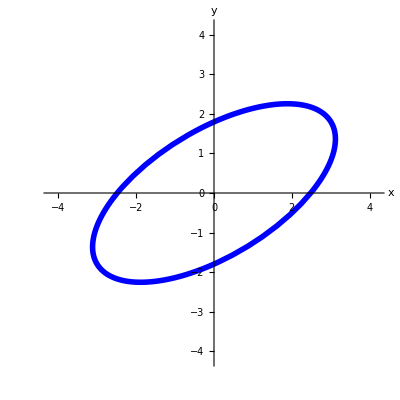

```mathematica
Clear[x,y,t];
{x[t_],y[t_]}={Cos[t],Sin[t]};
{tlow,thigh}={0,2 π};
ranger=1.2 Max[{xstretch,ystretch,1}];
ellipseplot=ParametricPlot[Transpose[A].{x[t],y[t]},{t,tlow,thigh},PlotStyle->{{Thickness[0.01],Blue}},PlotRange->{{-ranger,ranger},{-ranger,ranger}},AxesLabel->{"x","y"}]
```

Look at this plot of the aligner frame and its negatives:

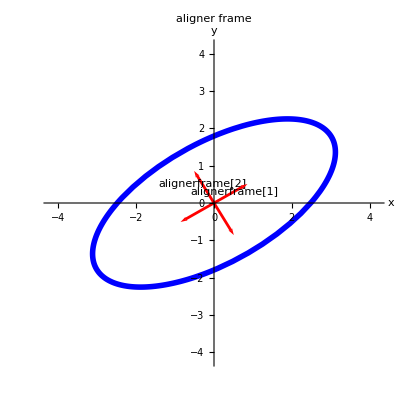

```mathematica
Show[ellipseplot,Vector[alignerframe[1],Tail->{0,0},VectorColor->Red],Vector[-alignerframe[1],Tail->{0,0},VectorColor->Red],Vector[alignerframe[2],Tail->{0,0},VectorColor->Red],Vector[-alignerframe[2],Tail->{0,0},VectorColor->Red],Graphics[Text["alignerframe[1]",0.6 alignerframe[1]]],Graphics[Text["alignerframe[2]",0.6 alignerframe[2]]],Axes->True,AxesLabel->{"x","y"},PlotRange->{{-ranger,ranger},{-ranger,ranger}},PlotLabel->"aligner frame"]
```

Do you think the outcome is an accident? 
Yes.......
No........
If not, explain your response.

#### L.27.ii)

Stay with the same set up as in part i) and look at this plot in which the unit hanger frame vectors have been multiplied by their associated stretch factors:

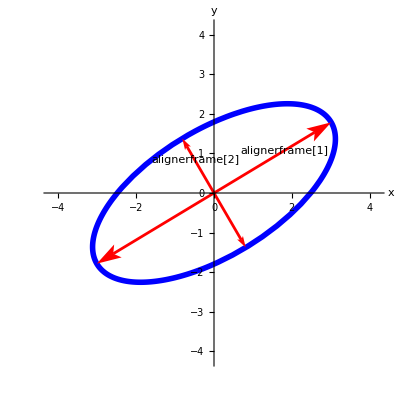

```mathematica
lastplot=Show[ellipseplot,Vector[xstretch alignerframe[1],Tail->{0,0},VectorColor->Red],Vector[-xstretch alignerframe[1],Tail->{0,0},VectorColor->Red],Vector[ystretch alignerframe[2],Tail->{0,0},VectorColor->Red],Vector[-ystretch alignerframe[2],Tail->{0,0},VectorColor->Red],Graphics[Text["alignerframe[1]",0.6 xstretch alignerframe[1]]],Graphics[Text["alignerframe[2]",0.6 ystretch alignerframe[2]]],Axes->True,AxesLabel->{"x","y"},PlotRange->{{-ranger,ranger},{-ranger,ranger}}]
```

Do you think the outcome is an accident? 
Yes.........
No.........
If not, explain your response.

#### L.27.iii)

Here's another look at the plot in part ii) above:

```mathematica
Show[lastplot]
```

-Graphics-

And look at the stretch factors used to make A:

```mathematica
{xstretch,ystretch}
```

{3.5,1.6}

Fill the blanks.
The length of the long axis of this ellipse measures out to ...........
The length of the short axis of this ellipse measures out to ...........
The area enclosed by this ellipse measures out to.........

#### L.28.i)

Here's a random 2D matrix 
              A = hanger.stretcher.aligner 
made through matrix maker ingredients.
The aligner is:

```mathematica
Clear[alignerframe]; 
s=Random[Real,{-1.5,1.5}]; 
{alignerframe[1],alignerframe[2]}=N[{{Cos[s],Sin[s]},{Cos[s+π/2],Sin[s+π/2]}}]; 
aligner={alignerframe[1],alignerframe[2]};
MatrixForm[aligner]
```

(0.810084 | -0.586314
0.586314 | 0.810084)

The stretcher is:

```mathematica
{xstretch,ystretch}={0.5 Random[Integer,{1,3}],0.4 Random[Integer,{1,2}]};
stretcher={{xstretch,0},{0,ystretch}}; 
MatrixForm[stretcher]
```

(0.5 | 0
0 | 0.8)

The hanger is:

```mathematica
Clear[hangerframe]; 
s=Random[Real,{-1.5,1.5}]; 
{hangerframe[1],hangerframe[2]}=N[{{Cos[s],Sin[s]},{Cos[s+π/2],Sin[s+π/2]}}]; 
hanger=Transpose[{hangerframe[1],hangerframe[2]}];
MatrixForm[hanger]
```

(0.812908 | 0.582393
-0.582393 | 0.812908)

The resulting matrix 
             A = hanger.stretcher.aligner 
is:

```mathematica
A=hanger.(stretcher.aligner); 
MatrixForm[A]
```

(0.602434 | 0.13912
0.145402 | 0.697551)

When you hit the unit circle centered at {0,0} with A^-1 you get this ellipse:

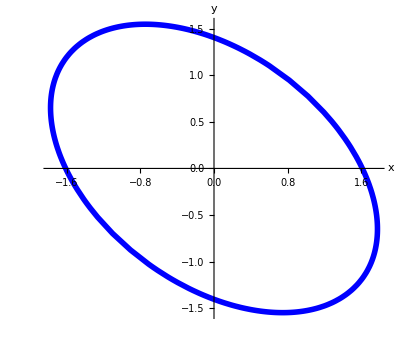

```mathematica
Clear[x,y,t];
{x[t_],y[t_]}={Cos[t],Sin[t]};
{tlow,thigh}={0,2 π};
ranger=1.2 Max[{xstretch,ystretch,1}]; 
ellipseplot=ParametricPlot[Inverse[A].{x[t],y[t]},{t,tlow,thigh},PlotStyle->{{Thickness[0.01],Blue}},PlotRange->All,AxesLabel->{"x","y"}]
```

Look at this plot of the aligner frame and its negatives:

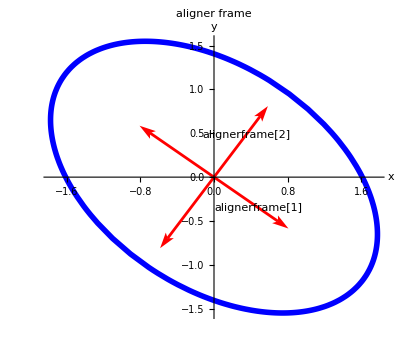

```mathematica
lastplot=Show[ellipseplot,Vector[alignerframe[1],Tail->{0,0},VectorColor->Red],Vector[-alignerframe[1],Tail->{0,0},VectorColor->Red],Vector[alignerframe[2],Tail->{0,0},VectorColor->Red],Vector[-alignerframe[2],Tail->{0,0},VectorColor->Red],Graphics[Text["alignerframe[1]",0.6 alignerframe[1]]],Graphics[Text["alignerframe[2]",0.6 alignerframe[2]]],Axes->True,AxesLabel->{"x","y"},PlotRange->All,PlotLabel->"aligner frame"]
```

Do you think the outcome is an accident? 
Yes.......
No........
If not, explain your response.

#### L.28.ii)

Here's another look at the plot in part i) above:

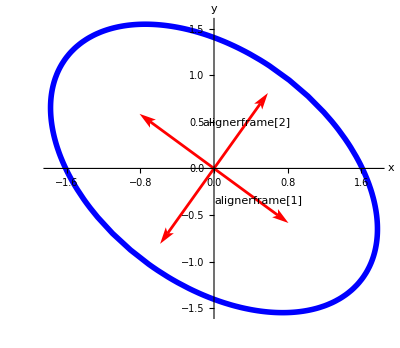

```mathematica
Show[lastplot,PlotLabel->None]
```

And look at the stretch factors used to make A:

```mathematica
{xstretch,ystretch}
```

{0.5,0.8}

Fill the blanks.
The length of the long axis of this ellipse measures out to ...........
The length of the short axis of this ellipse measures out to ...........
The area enclosed by this ellipse measures out to.........